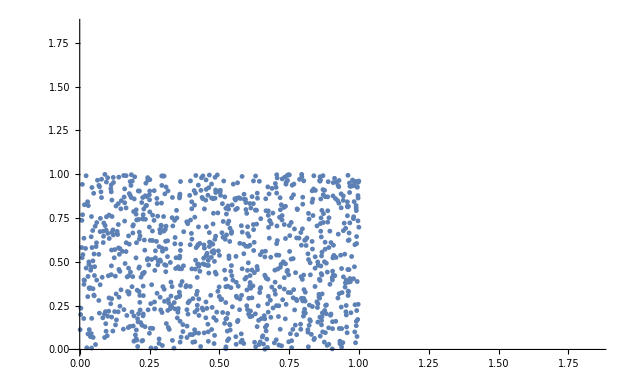

```mathematica
data1 = {0.42659327387809753,0.4741353988647461,0.2401113510131836,0.8730306625366211,0.7752370834350586,0.2865743637084961,0.6843862533569336,0.1835165023803711,0.9363088607788086,0.032607078552246094,0.4997549057006836,0.3025960922241211,0.3434743881225586,0.4622335433959961,0.4362173080444336,0.9802694320678711,0.7467336654663086,0.3254537582397461,0.2437734603881836,0.9665365219116211,0.8960866928100586,0.3722677230834961,0.6724233627319336,0.011397361755371094,0.5415334701538086,0.3526754379272461,0.4721670150756836,0.8648519515991211,0.4330739974975586,0.016676902770996094,0.3930044174194336,0.2769002914428711,0.3207082748413086,0.1142721176147461,0.1849355697631836,0.9975423812866211,0.9544363021850586,0.3954610824584961,0.5979604721069336,0.7767782211303711,0.0842580795288086,0.6102437973022461,0.3820791244506836,0.3646078109741211,0.4601736068725586,0.5086202621459961,0.2872915267944336,0.5110311508178711,0.8321828842163086,0.8405904769897461,0.0635976791381836,0.9660482406616211,0.9502859115600586,0.3561544418334961,0.4609975814819336,0.4796590805053711,0.5644826889038086,0.8053121566772461,0.2294912338256836,0.8018636703491211,0.4247732162475586,0.9380636215209961,0.1190786361694336,0.6826620101928711,0.2811574935913086,0.5044088363647461,0.8797597885131836,0.8720541000366211,0.8836355209350586,0.2543478012084961,0.2615346908569336,0.1200399398803711,0.9822072982788086,0.9378805160522461,0.014403343200683594,0.1766195297241211,0.3268728256225586,0.3050069808959961,0.8883657455444336,0.7917928695678711,0.6676321029663086,0.1057271957397461,0.6334218978881836,0.7155599594116211,0.7544851303100586,0.0900411605834961,0.9995718002319336,0.6979207992553711,0.3374319076538086,0.007948875427246094,0.7368154525756836,0.4888753890991211,0.1664724349975586,0.6094503402709961,0.5951528549194336,0.8384237289428711,0.9916067123413086,0.6445455551147461,0.3245840072631836,0.4965658187866211,0.5628347396850586,0.8632345199584961,0.6751089096069336,0.2133016586303711,0.6301565170288086,0.015517234802246094,0.3967275619506836,0.7386312484741211,0.9435720443725586,0.8513936996459961,0.2394399642944336,0.8225545883178711,0.2530813217163086,0.1208639144897461,0.9532461166381836,0.2150716781616211,0.3086843490600586,0.5739278793334961,0.2881460189819336,0.6661825180053711,0.8603811264038086,0.9605855941772461,0.9941396713256836,0.9258871078491211,0.6581716537475586,0.030837059020996094,0.8212270736694336,0.7441854476928711,0.4520559310913086,0.5346822738647461,0.5194082260131836,0.8710775375366211,0.9920339584350586,0.2221212387084961,0.8386831283569336,0.056563377380371094,0.028105735778808594,0.8431539535522461,0.5290517807006836,0.050642967224121094,0.3102712631225586,0.1477804183959961,0.3405141830444336,0.6033163070678711,0.5885305404663086,0.8860006332397461,0.023070335388183594,0.4645833969116211,0.6128835678100586,0.8078145980834961,0.3267202377319336,0.3844442367553711,0.1333303451538086,0.6632223129272461,0.0014638900756835938,0.1128988265991211,0.8998708724975586,0.2022237777709961,0.7973012924194336,0.3999471664428711,0.6625051498413086,0.1748189926147461,0.4642324447631836,0.9955892562866211,0.1712331771850586,0.3310079574584961,0.7522573471069336,0.6498250961303711,0.1760549545288086,0.4207906723022461,0.4113759994506836,0.1126546859741211,0.4269704818725586,0.1941671371459961,0.1915884017944336,0.1340780258178711,0.6739797592163086,0.4011373519897461,0.8428945541381836,0.4640951156616211,0.6670827865600586,0.7917013168334961,0.1152944564819336,0.8527059555053711,0.1562795639038086,0.1158590316772461,0.7587881088256836,0.049910545349121094,0.8915700912475586,0.1236104965209961,0.5233755111694336,0.8057088851928711,0.6229543685913086,0.5649557113647461,0.1590566635131836,0.8701009750366211,0.1004323959350586,0.1898946762084961,0.4158315658569336,0.9930868148803711,0.0740041732788086,0.7484273910522461,0.043700218200683594,0.9246664047241211,0.2936697006225586,0.9905538558959961,0.7926626205444336,0.4148397445678711,0.5094289779663086,0.6662740707397461,0.4127187728881836,0.2136068344116211,0.4712820053100586,0.5255880355834961,0.6538686752319336,0.0709676742553711,0.9292287826538086,0.3184957504272461,0.2661123275756836,0.7369222640991211,0.6332693099975586,0.7949972152709961,0.9994497299194336,0.9614706039428711,0.3334035873413086,0.7050924301147461,0.6038808822631836,0.4946126937866211,0.7796316146850586,0.7987813949584961,0.8294057846069336,0.0863485336303711,0.7219533920288086,0.8260641098022461,0.4260244369506836,0.4866781234741211,0.9103689193725586,0.5369405746459961,0.1437368392944336,0.4456014633178711,0.0948781967163086,0.6814107894897461,0.7325429916381836,0.7131185531616211,0.025481224060058594,0.009474754333496094,0.9424428939819336,0.039229393005371094,0.4521780014038086,0.2711324691772461,0.5234365463256836,0.1739339828491211,0.1249685287475586,0.2163839340209961,0.2255239486694336,0.8672323226928711,0.7938528060913086,0.5952291488647461,0.7987051010131836,0.8691244125366211,0.2088308334350586,0.1576681137084961,0.9929800033569336,0.9296102523803711,0.1199026107788086,0.6537008285522461,0.5583486557006836,0.7986898422241211,0.2770681381225586,0.8333272933959961,0.2448110580444336,0.2263631820678711,0.4303274154663086,0.4465475082397461,0.8023672103881836,0.9626302719116211,0.3296804428100586,0.2433614730834961,0.9810171127319336,0.7574911117553711,0.7251272201538086,0.9737691879272461,0.5307607650756836,0.3609457015991211,0.3666677474975586,0.3877706527709961,0.2015981674194336,0.5229940414428711,0.004302024841308594,0.2353658676147461,0.7435293197631836,0.9936361312866211,0.3880300521850586,0.2665548324584961,0.9065542221069336,0.5228719711303711,0.2678518295288086,0.2313375473022461,0.4406728744506836,0.8607015609741211,0.3937673568725586,0.8797140121459961,0.0958852767944336,0.7571249008178711,0.5157766342163086,0.9616842269897461,0.6221914291381836,0.9621419906616211,0.3838796615600586,0.2272481918334961,0.7695913314819336,0.2257528305053711,0.7480764389038086,0.4264059066772461,0.2880849838256836,0.2979574203491211,0.3583669662475586,0.3091573715209961,0.9276723861694336,0.9287557601928711,0.9647512435913086,0.6255025863647461,0.4383535385131836,0.8681478500366211,0.3172292709350586,0.1254415512084961,0.5701284408569336,0.8661336898803711,0.1658010482788086,0.5589742660522461,0.0729970932006836,0.6727132797241211,0.2604665756225586,0.6761007308959961,0.6969594955444336,0.037886619567871094,0.3512258529663086,0.2268209457397461,0.1920156478881836,0.7116537094116211,0.1880788803100586,0.9611349105834961,0.3081655502319336,0.4440145492553711,0.5210256576538086,0.6290426254272461,0.7954092025756836,0.9849691390991211,0.1000661849975586,0.9805440902709961,0.4037466049194336,0.0845174789428711,0.6752004623413086,0.7656393051147461,0.8831777572631836,0.4926595687866211,0.9964284896850586,0.7343282699584961,0.9837026596069336,0.9593954086303711,0.8137502670288086,0.6366109848022461,0.4553213119506836,0.2347249984741211,0.8771657943725586,0.2224874496459961,0.048033714294433594,0.0686483383178711,0.9366750717163086,0.2419576644897461,0.5118398666381836,0.2111654281616211,0.7422780990600586,0.4450216293334961,0.5967397689819336,0.4122762680053711,0.043974876403808594,0.5816793441772461,0.052733421325683594,0.4219808578491211,0.5917654037475586,0.4019308090209961,0.6298208236694336,0.9902791976928711,0.1356496810913086,0.6557760238647461,0.0780019760131836,0.8671712875366211,0.4256277084350586,0.0932149887084961,0.1472768783569336,0.8026571273803711,0.2116994857788086,0.4642477035522461,0.5876455307006836,0.5467367172241211,0.2438650131225586,0.5188741683959961,0.1491079330444336,0.8494100570678711,0.2721242904663086,0.007094383239746094,0.5816640853881836,0.4606771469116211,0.046477317810058594,0.6789083480834961,0.6353139877319336,0.1305379867553711,0.3169240951538086,0.2843160629272461,0.060057640075683594,0.6089925765991211,0.8334646224975586,0.5733175277709961,0.6058950424194336,0.6460409164428711,0.3460988998413086,0.2959127426147461,0.022826194763183594,0.9916830062866211,0.6048269271850586,0.2021017074584961,0.060851097106933594,0.3959188461303711,0.3596487045288086,0.041884422302246094,0.4699697494506836,0.6087484359741211,0.3605642318725586,0.5652608871459961,1.8215179443359375E-4,0.3801717758178711,0.3575735092163086,0.5222311019897461,0.4014883041381836,0.4601888656616211,0.1006765365600586,0.6627950668334961,0.4238882064819336,0.5987997055053711,0.3398733139038086,0.7369527816772461,0.8173818588256836,0.5460042953491211,0.8251638412475586,0.4947042465209961,0.3319692611694336,0.051802635192871094,0.3065481185913086,0.6860494613647461,0.7176504135131836,0.8661947250366211,0.5340261459350586,0.060988426208496094,0.7244253158569336,0.7391805648803711,0.2575979232788086,0.3695211410522461,0.1022939682006836,0.4207601547241211,0.2272634506225586,0.3616476058959961,0.6012563705444336,0.6609334945678711,0.1930227279663086,0.7873678207397461,0.9713125228881836,0.2097005844116211,0.9048757553100586,0.3966817855834961,0.9624624252319336,0.8170614242553711,0.1128225326538086,0.9395895004272461,0.3247060775756836,0.2330160140991211,0.5668630599975586,0.1660909652709961,0.8080434799194336,0.2075643539428711,0.016997337341308594,0.8261861801147461,0.1624746322631836,0.4907064437866211,0.2132253646850586,0.6698751449584961,0.1379995346069336,0.8324422836303711,0.9055471420288086,0.4471578598022461,0.4846181869506836,0.9827718734741211,0.8439626693725586,0.9080343246459961,0.9523305892944336,0.6916952133178711,0.7784719467163086,0.8025045394897461,0.2911367416381836,0.7092123031616211,0.4590749740600586,0.8805685043334961,0.2510366439819336,0.7853231430053711,0.6357717514038086,0.8922262191772461,0.5820302963256836,0.6700277328491211,0.058562278747558594,0.5874776840209961,0.034117698669433594,0.1133260726928711,0.4774465560913086,0.7163228988647461,0.3572988510131836,0.8652181625366211,0.6424245834350586,0.028761863708496094,0.3015737533569336,0.6757040023803711,0.3034963607788086,0.2747945785522461,0.6169424057006836,0.2947835922241211,0.2106618881225586,0.2044210433959961,0.053404808044433594,0.4724569320678711,0.1139211654663086,0.5676412582397461,0.3609609603881836,0.9587240219116211,0.7632741928100586,0.1144552230834961,0.2896108627319336,0.5035848617553711,0.9087209701538086,0.5948629379272461,0.5893545150756836,0.8570394515991211,0.3002614974975586,0.7588644027709961,0.010191917419433594,0.7690877914428711,0.6878957748413086,0.3564596176147461,0.3021230697631836,0.9897298812866211,0.8216238021850586,0.1376485824584961,0.2151479721069336,0.2689657211303711,0.4514455795288086,0.8524312973022461,0.4992666244506836,0.3567953109741211,0.3273611068725586,0.2508077621459961,0.9044790267944336,0.0032186508178710938,0.1993703842163086,0.0827779769897461,0.1807851791381836,0.9582357406616211,0.8174734115600586,0.0983419418334961,0.0781850814819336,0.9718465805053711,0.9316701889038086,0.047499656677246094,0.3466787338256836,0.7940511703491211,0.2919607162475586,0.6802511215209961,0.7362661361694336,0.1748495101928711,0.6483449935913086,0.7465963363647461,0.9969472885131836,0.8642416000366211,0.7508230209350586,0.9965353012084961,0.8787221908569336,0.6122274398803711,0.3493947982788086,0.1800680160522461,0.1315908432006836,0.1688070297241211,0.1940603256225586,0.047194480895996094,0.5055532455444336,0.2839803695678711,0.034819602966308594,0.3479146957397461,0.7506093978881836,0.7077474594116211,0.6216726303100586,0.8322286605834961,0.6167593002319336,0.1901082992553711,0.7046194076538086,0.2501363754272461,0.8540029525756836,0.4810628890991211,0.033659934997558594,0.3516378402709961,0.2123403549194336,0.3306112289428711,0.3587942123413086,0.8867330551147461,0.4417715072631836,0.4887533187866211,0.4300222396850586,0.6054220199584961,0.2922964096069336,0.7054891586303711,0.9973440170288086,0.2577047348022461,0.5139150619506836,0.7308187484741211,0.8107595443725586,0.5935811996459961,0.8566274642944336,0.3147420883178711,0.6202688217163086,0.3630514144897461,0.0704336166381836,0.2072591781616211,0.1758718490600586,0.3161153793334961,0.9053335189819336,0.1583700180053711,0.2275686264038086,0.2027730941772461,0.1113271713256836,0.9180746078491211,0.5253591537475586,0.7730245590209961,0.4384145736694336,0.2363729476928711,0.8192434310913086,0.7768697738647461,0.6365957260131836,0.8632650375366211,0.8592214584350586,0.9643087387084961,0.4558706283569336,0.5487508773803711,0.3952932357788086,0.0853414535522461,0.6462392807006836,0.042830467224121094,0.1774587631225586,0.8899679183959961,0.9577016830444336,0.0955038070678711,0.9557180404663086,0.1281881332397461,0.1402578353881836,0.4567708969116211,0.4800710678100586,0.5500020980834961,0.9439077377319336,0.8766317367553711,0.5005178451538086,0.9054098129272461,0.1186513900756836,0.1050863265991211,0.7670583724975586,0.9444112777709961,0.4144887924194336,0.8921346664428711,0.029692649841308594,0.4170064926147461,0.5814199447631836,0.9877767562866211,0.038420677185058594,0.0731954574584961,0.3694448471069336,0.1420125961303711,0.5432424545288086,0.6629781723022461,0.5285634994506836,0.1048421859741211,0.2941579818725586,0.9363546371459961,0.8087759017944336,0.6262655258178711,0.041167259216308594,0.6433248519897461,0.9600820541381836,0.4562826156616211,0.5342702865600586,0.5338888168334961,0.7324819564819336,0.3448934555053711,0.5234670639038086,0.3580465316772461,0.8759756088256836,0.042098045349121094,0.7587575912475586,0.8657979965209961,0.1405630111694336,0.2978963851928711,0.9901418685913086,0.8071432113647461,0.2762441635131836,0.8622884750366211,0.9676198959350586,0.9320821762084961,0.033019065856933594,0.4852743148803711,0.4411916732788086,0.9906148910522461,0.1608877182006836,0.9168539047241211,0.1608572006225586,0.7327413558959961,0.4098501205444336,0.9070272445678711,0.8766164779663086,0.9084615707397461,0.5299062728881836,0.2057943344116211,0.3384695053100586,0.2677755355834961,0.2710561752319336,0.5631551742553711,0.2964162826538086,0.5606832504272461,0.3832998275756836,0.7291097640991211,0.5004568099975586,0.5371847152709961,0.6166372299194336,0.4536581039428711,0.7005910873413086,0.9472799301147461,0.7210683822631836,0.4868001937866211,0.6468191146850586,0.5409688949584961,0.4465932846069336,0.5785360336303711,0.0891408920288086,0.0682516098022461,0.5432119369506836,0.4788656234741211,0.7775564193725586,0.2791280746459961,0.7609243392944336,0.9377889633178711,0.4620656967163086,0.9235982894897461,0.8497304916381836,0.7053060531616211,0.8926687240600586,0.7516622543334961,0.5596303939819336,0.5314168930053711,0.8193655014038086,0.5133199691772461,0.6406240463256836,0.1661214828491211,0.9921560287475586,0.9585714340209961,0.8427114486694336,0.3594198226928711,0.1610403060913086,0.8374166488647461,0.9158926010131836,0.8613119125366211,0.0760183334350586,0.8998556137084961,0.6101675033569336,0.4217977523803711,0.4870901107788086,0.8958883285522461,0.6755361557006836,0.7908773422241211,0.1442556381225586,0.5755147933959961,0.8619985580444336,0.7185506820678711,0.7975149154663086,0.6887350082397461,0.9195547103881836,0.9548177719116211,0.1968679428100586,0.9855489730834961,0.5982046127319336,0.2496786117553711,0.0923147201538086,0.2159566879272461,0.6479482650756836,0.3531332015991211,0.2338552474975586,0.1299581527709961,0.8187856674194336,0.015181541442871094,0.3714895248413086,0.4775533676147461,0.8607168197631836,0.9858236312866211,0.2552175521850586,0.008742332458496094,0.5237417221069336,0.015059471130371094,0.6350393295288086,0.4735250473022461,0.5578603744506836,0.8528890609741211,0.2609548568725586,0.6219015121459961,0.7130727767944336,0.2493124008178711,0.8829641342163086,0.2038717269897461,0.7393789291381836,0.9543294906616211,0.2510671615600586,0.9694356918334961,0.3867788314819336,0.7179403305053711,0.1152639389038086,0.6685934066772461,0.4052724838256836,0.2901449203491211,0.2255544662475586,0.051344871520996094,0.5448598861694336,0.4209432601928711,0.3319387435913086,0.8676900863647461,0.5555410385131836,0.8603353500366211,0.1844167709350586,0.8676290512084961,0.1873159408569336,0.3583211898803711,0.5329885482788086,0.8011617660522461,0.1901845932006836,0.6649007797241211,0.1276540756225586,0.4182882308959961,0.3141469955444336,0.5300741195678711,0.7184133529663086,0.4690084457397461,0.3092031478881836,0.7038412094116211,0.055266380310058594,0.7033224105834961,0.9253530502319336,0.9362020492553711,0.8882131576538086,0.8712301254272461,0.9125967025756836,0.9771566390991211,0.9672536849975586,0.7227315902709961,0.020934104919433594,0.5767049789428711,0.042387962341308594,0.007826805114746094,3.6525726318359375E-4,0.4848470687866211,0.8636159896850586,0.4765157699584961,0.6008901596069336,0.4515829086303711,0.1809377670288086,0.8787984848022461,0.5725088119506836,0.2269124984741211,0.7443532943725586,0.9646749496459961,0.6652212142944336,0.5608358383178711,0.3038625717163086,0.4841451644897461,0.6290273666381836,0.2033529281616211,0.6094655990600586,0.1872091293334961,0.2139272689819336,0.9044637680053711,0.4111623764038086,0.8238668441772461,0.1699209213256836,0.4141683578491211,0.4589529037475586,0.1441183090209961,0.2470083236694336,0.4824666976928711,0.5028371810913086,0.8979635238647461,0.1951894760131836,0.8593587875366211,0.2928152084350586,0.8354024887084961,0.7644643783569336,0.2948446273803711,0.5788869857788086,0.7064352035522461,0.7048330307006836,0.5389242172241211,0.1110525131225586,0.2610616683959961,0.7662954330444336,0.3415975570678711,0.6393117904663086,0.2492818832397461,0.6988515853881836,0.4528646469116211,0.9136648178100586,0.4210958480834961,0.2525014877319336,0.6227254867553711,0.6841115951538086,0.5265035629272461,0.1772451400756836,0.6011800765991211,0.7006521224975586,0.3155050277709961,0.2230825424194336,0.1382284164428711,0.7132863998413086,0.5381002426147461,0.1400136947631836,0.9838705062866211,0.4720144271850586,0.9442892074584961,0.6780385971069336,0.8881063461303711,0.7268362045288086,0.2840719223022461,0.5871572494506836,0.6009359359741211,0.2277517318725586,0.3074483871459961,0.6173696517944336,0.8723592758178711,0.7247610092163086,0.7644186019897461,0.5186758041381836,0.4523763656616211,0.9678640365600586,0.4049825668334961,0.041075706481933594,0.0909872055053711,0.7070608139038086,0.9791402816772461,0.9345693588256836,0.5381917953491211,0.6923513412475586,0.2368917465209961,0.9491567611694336,0.5439901351928711,0.6737356185913086,0.9282369613647461,0.8348379135131836,0.8583822250366211,0.4012136459350586,0.8031759262084961,0.3416128158569336,0.2313680648803711,0.6247854232788086,0.6117086410522461,0.2194814682006836,0.4129476547241211,0.0944509506225586,0.1038351058959961,0.2184438705444336,0.1531209945678711,0.5602102279663086,0.029555320739746094,0.0885000228881836,0.2018880844116211,0.7720632553100586,0.1388692855834961,0.5796499252319336,0.3092489242553711,0.4800100326538086,0.1817770004272461,0.4418935775756836,0.2252035140991211,0.4340505599975586,0.9082784652709961,0.4252309799194336,0.6997518539428711,0.3841848373413086,0.0683736801147461,0.2796621322631836,0.4828939437866211,0.0804128646850586,0.4120626449584961,0.7551870346069336};

data2 = {0.4741353988647461,0.2401113510131836,0.8730306625366211,0.7752370834350586,0.2865743637084961,0.6843862533569336,0.1835165023803711,0.9363088607788086,0.032607078552246094,0.4997549057006836,0.3025960922241211,0.3434743881225586,0.4622335433959961,0.4362173080444336,0.9802694320678711,0.7467336654663086,0.3254537582397461,0.2437734603881836,0.9665365219116211,0.8960866928100586,0.3722677230834961,0.6724233627319336,0.011397361755371094,0.5415334701538086,0.3526754379272461,0.4721670150756836,0.8648519515991211,0.4330739974975586,0.016676902770996094,0.3930044174194336,0.2769002914428711,0.3207082748413086,0.1142721176147461,0.1849355697631836,0.9975423812866211,0.9544363021850586,0.3954610824584961,0.5979604721069336,0.7767782211303711,0.0842580795288086,0.6102437973022461,0.3820791244506836,0.3646078109741211,0.4601736068725586,0.5086202621459961,0.2872915267944336,0.5110311508178711,0.8321828842163086,0.8405904769897461,0.0635976791381836,0.9660482406616211,0.9502859115600586,0.3561544418334961,0.4609975814819336,0.4796590805053711,0.5644826889038086,0.8053121566772461,0.2294912338256836,0.8018636703491211,0.4247732162475586,0.9380636215209961,0.1190786361694336,0.6826620101928711,0.2811574935913086,0.5044088363647461,0.8797597885131836,0.8720541000366211,0.8836355209350586,0.2543478012084961,0.2615346908569336,0.1200399398803711,0.9822072982788086,0.9378805160522461,0.014403343200683594,0.1766195297241211,0.3268728256225586,0.3050069808959961,0.8883657455444336,0.7917928695678711,0.6676321029663086,0.1057271957397461,0.6334218978881836,0.7155599594116211,0.7544851303100586,0.0900411605834961,0.9995718002319336,0.6979207992553711,0.3374319076538086,0.007948875427246094,0.7368154525756836,0.4888753890991211,0.1664724349975586,0.6094503402709961,0.5951528549194336,0.8384237289428711,0.9916067123413086,0.6445455551147461,0.3245840072631836,0.4965658187866211,0.5628347396850586,0.8632345199584961,0.6751089096069336,0.2133016586303711,0.6301565170288086,0.015517234802246094,0.3967275619506836,0.7386312484741211,0.9435720443725586,0.8513936996459961,0.2394399642944336,0.8225545883178711,0.2530813217163086,0.1208639144897461,0.9532461166381836,0.2150716781616211,0.3086843490600586,0.5739278793334961,0.2881460189819336,0.6661825180053711,0.8603811264038086,0.9605855941772461,0.9941396713256836,0.9258871078491211,0.6581716537475586,0.030837059020996094,0.8212270736694336,0.7441854476928711,0.4520559310913086,0.5346822738647461,0.5194082260131836,0.8710775375366211,0.9920339584350586,0.2221212387084961,0.8386831283569336,0.056563377380371094,0.028105735778808594,0.8431539535522461,0.5290517807006836,0.050642967224121094,0.3102712631225586,0.1477804183959961,0.3405141830444336,0.6033163070678711,0.5885305404663086,0.8860006332397461,0.023070335388183594,0.4645833969116211,0.6128835678100586,0.8078145980834961,0.3267202377319336,0.3844442367553711,0.1333303451538086,0.6632223129272461,0.0014638900756835938,0.1128988265991211,0.8998708724975586,0.2022237777709961,0.7973012924194336,0.3999471664428711,0.6625051498413086,0.1748189926147461,0.4642324447631836,0.9955892562866211,0.1712331771850586,0.3310079574584961,0.7522573471069336,0.6498250961303711,0.1760549545288086,0.4207906723022461,0.4113759994506836,0.1126546859741211,0.4269704818725586,0.1941671371459961,0.1915884017944336,0.1340780258178711,0.6739797592163086,0.4011373519897461,0.8428945541381836,0.4640951156616211,0.6670827865600586,0.7917013168334961,0.1152944564819336,0.8527059555053711,0.1562795639038086,0.1158590316772461,0.7587881088256836,0.049910545349121094,0.8915700912475586,0.1236104965209961,0.5233755111694336,0.8057088851928711,0.6229543685913086,0.5649557113647461,0.1590566635131836,0.8701009750366211,0.1004323959350586,0.1898946762084961,0.4158315658569336,0.9930868148803711,0.0740041732788086,0.7484273910522461,0.043700218200683594,0.9246664047241211,0.2936697006225586,0.9905538558959961,0.7926626205444336,0.4148397445678711,0.5094289779663086,0.6662740707397461,0.4127187728881836,0.2136068344116211,0.4712820053100586,0.5255880355834961,0.6538686752319336,0.0709676742553711,0.9292287826538086,0.3184957504272461,0.2661123275756836,0.7369222640991211,0.6332693099975586,0.7949972152709961,0.9994497299194336,0.9614706039428711,0.3334035873413086,0.7050924301147461,0.6038808822631836,0.4946126937866211,0.7796316146850586,0.7987813949584961,0.8294057846069336,0.0863485336303711,0.7219533920288086,0.8260641098022461,0.4260244369506836,0.4866781234741211,0.9103689193725586,0.5369405746459961,0.1437368392944336,0.4456014633178711,0.0948781967163086,0.6814107894897461,0.7325429916381836,0.7131185531616211,0.025481224060058594,0.009474754333496094,0.9424428939819336,0.039229393005371094,0.4521780014038086,0.2711324691772461,0.5234365463256836,0.1739339828491211,0.1249685287475586,0.2163839340209961,0.2255239486694336,0.8672323226928711,0.7938528060913086,0.5952291488647461,0.7987051010131836,0.8691244125366211,0.2088308334350586,0.1576681137084961,0.9929800033569336,0.9296102523803711,0.1199026107788086,0.6537008285522461,0.5583486557006836,0.7986898422241211,0.2770681381225586,0.8333272933959961,0.2448110580444336,0.2263631820678711,0.4303274154663086,0.4465475082397461,0.8023672103881836,0.9626302719116211,0.3296804428100586,0.2433614730834961,0.9810171127319336,0.7574911117553711,0.7251272201538086,0.9737691879272461,0.5307607650756836,0.3609457015991211,0.3666677474975586,0.3877706527709961,0.2015981674194336,0.5229940414428711,0.004302024841308594,0.2353658676147461,0.7435293197631836,0.9936361312866211,0.3880300521850586,0.2665548324584961,0.9065542221069336,0.5228719711303711,0.2678518295288086,0.2313375473022461,0.4406728744506836,0.8607015609741211,0.3937673568725586,0.8797140121459961,0.0958852767944336,0.7571249008178711,0.5157766342163086,0.9616842269897461,0.6221914291381836,0.9621419906616211,0.3838796615600586,0.2272481918334961,0.7695913314819336,0.2257528305053711,0.7480764389038086,0.4264059066772461,0.2880849838256836,0.2979574203491211,0.3583669662475586,0.3091573715209961,0.9276723861694336,0.9287557601928711,0.9647512435913086,0.6255025863647461,0.4383535385131836,0.8681478500366211,0.3172292709350586,0.1254415512084961,0.5701284408569336,0.8661336898803711,0.1658010482788086,0.5589742660522461,0.0729970932006836,0.6727132797241211,0.2604665756225586,0.6761007308959961,0.6969594955444336,0.037886619567871094,0.3512258529663086,0.2268209457397461,0.1920156478881836,0.7116537094116211,0.1880788803100586,0.9611349105834961,0.3081655502319336,0.4440145492553711,0.5210256576538086,0.6290426254272461,0.7954092025756836,0.9849691390991211,0.1000661849975586,0.9805440902709961,0.4037466049194336,0.0845174789428711,0.6752004623413086,0.7656393051147461,0.8831777572631836,0.4926595687866211,0.9964284896850586,0.7343282699584961,0.9837026596069336,0.9593954086303711,0.8137502670288086,0.6366109848022461,0.4553213119506836,0.2347249984741211,0.8771657943725586,0.2224874496459961,0.048033714294433594,0.0686483383178711,0.9366750717163086,0.2419576644897461,0.5118398666381836,0.2111654281616211,0.7422780990600586,0.4450216293334961,0.5967397689819336,0.4122762680053711,0.043974876403808594,0.5816793441772461,0.052733421325683594,0.4219808578491211,0.5917654037475586,0.4019308090209961,0.6298208236694336,0.9902791976928711,0.1356496810913086,0.6557760238647461,0.0780019760131836,0.8671712875366211,0.4256277084350586,0.0932149887084961,0.1472768783569336,0.8026571273803711,0.2116994857788086,0.4642477035522461,0.5876455307006836,0.5467367172241211,0.2438650131225586,0.5188741683959961,0.1491079330444336,0.8494100570678711,0.2721242904663086,0.007094383239746094,0.5816640853881836,0.4606771469116211,0.046477317810058594,0.6789083480834961,0.6353139877319336,0.1305379867553711,0.3169240951538086,0.2843160629272461,0.060057640075683594,0.6089925765991211,0.8334646224975586,0.5733175277709961,0.6058950424194336,0.6460409164428711,0.3460988998413086,0.2959127426147461,0.022826194763183594,0.9916830062866211,0.6048269271850586,0.2021017074584961,0.060851097106933594,0.3959188461303711,0.3596487045288086,0.041884422302246094,0.4699697494506836,0.6087484359741211,0.3605642318725586,0.5652608871459961,1.8215179443359375E-4,0.3801717758178711,0.3575735092163086,0.5222311019897461,0.4014883041381836,0.4601888656616211,0.1006765365600586,0.6627950668334961,0.4238882064819336,0.5987997055053711,0.3398733139038086,0.7369527816772461,0.8173818588256836,0.5460042953491211,0.8251638412475586,0.4947042465209961,0.3319692611694336,0.051802635192871094,0.3065481185913086,0.6860494613647461,0.7176504135131836,0.8661947250366211,0.5340261459350586,0.060988426208496094,0.7244253158569336,0.7391805648803711,0.2575979232788086,0.3695211410522461,0.1022939682006836,0.4207601547241211,0.2272634506225586,0.3616476058959961,0.6012563705444336,0.6609334945678711,0.1930227279663086,0.7873678207397461,0.9713125228881836,0.2097005844116211,0.9048757553100586,0.3966817855834961,0.9624624252319336,0.8170614242553711,0.1128225326538086,0.9395895004272461,0.3247060775756836,0.2330160140991211,0.5668630599975586,0.1660909652709961,0.8080434799194336,0.2075643539428711,0.016997337341308594,0.8261861801147461,0.1624746322631836,0.4907064437866211,0.2132253646850586,0.6698751449584961,0.1379995346069336,0.8324422836303711,0.9055471420288086,0.4471578598022461,0.4846181869506836,0.9827718734741211,0.8439626693725586,0.9080343246459961,0.9523305892944336,0.6916952133178711,0.7784719467163086,0.8025045394897461,0.2911367416381836,0.7092123031616211,0.4590749740600586,0.8805685043334961,0.2510366439819336,0.7853231430053711,0.6357717514038086,0.8922262191772461,0.5820302963256836,0.6700277328491211,0.058562278747558594,0.5874776840209961,0.034117698669433594,0.1133260726928711,0.4774465560913086,0.7163228988647461,0.3572988510131836,0.8652181625366211,0.6424245834350586,0.028761863708496094,0.3015737533569336,0.6757040023803711,0.3034963607788086,0.2747945785522461,0.6169424057006836,0.2947835922241211,0.2106618881225586,0.2044210433959961,0.053404808044433594,0.4724569320678711,0.1139211654663086,0.5676412582397461,0.3609609603881836,0.9587240219116211,0.7632741928100586,0.1144552230834961,0.2896108627319336,0.5035848617553711,0.9087209701538086,0.5948629379272461,0.5893545150756836,0.8570394515991211,0.3002614974975586,0.7588644027709961,0.010191917419433594,0.7690877914428711,0.6878957748413086,0.3564596176147461,0.3021230697631836,0.9897298812866211,0.8216238021850586,0.1376485824584961,0.2151479721069336,0.2689657211303711,0.4514455795288086,0.8524312973022461,0.4992666244506836,0.3567953109741211,0.3273611068725586,0.2508077621459961,0.9044790267944336,0.0032186508178710938,0.1993703842163086,0.0827779769897461,0.1807851791381836,0.9582357406616211,0.8174734115600586,0.0983419418334961,0.0781850814819336,0.9718465805053711,0.9316701889038086,0.047499656677246094,0.3466787338256836,0.7940511703491211,0.2919607162475586,0.6802511215209961,0.7362661361694336,0.1748495101928711,0.6483449935913086,0.7465963363647461,0.9969472885131836,0.8642416000366211,0.7508230209350586,0.9965353012084961,0.8787221908569336,0.6122274398803711,0.3493947982788086,0.1800680160522461,0.1315908432006836,0.1688070297241211,0.1940603256225586,0.047194480895996094,0.5055532455444336,0.2839803695678711,0.034819602966308594,0.3479146957397461,0.7506093978881836,0.7077474594116211,0.6216726303100586,0.8322286605834961,0.6167593002319336,0.1901082992553711,0.7046194076538086,0.2501363754272461,0.8540029525756836,0.4810628890991211,0.033659934997558594,0.3516378402709961,0.2123403549194336,0.3306112289428711,0.3587942123413086,0.8867330551147461,0.4417715072631836,0.4887533187866211,0.4300222396850586,0.6054220199584961,0.2922964096069336,0.7054891586303711,0.9973440170288086,0.2577047348022461,0.5139150619506836,0.7308187484741211,0.8107595443725586,0.5935811996459961,0.8566274642944336,0.3147420883178711,0.6202688217163086,0.3630514144897461,0.0704336166381836,0.2072591781616211,0.1758718490600586,0.3161153793334961,0.9053335189819336,0.1583700180053711,0.2275686264038086,0.2027730941772461,0.1113271713256836,0.9180746078491211,0.5253591537475586,0.7730245590209961,0.4384145736694336,0.2363729476928711,0.8192434310913086,0.7768697738647461,0.6365957260131836,0.8632650375366211,0.8592214584350586,0.9643087387084961,0.4558706283569336,0.5487508773803711,0.3952932357788086,0.0853414535522461,0.6462392807006836,0.042830467224121094,0.1774587631225586,0.8899679183959961,0.9577016830444336,0.0955038070678711,0.9557180404663086,0.1281881332397461,0.1402578353881836,0.4567708969116211,0.4800710678100586,0.5500020980834961,0.9439077377319336,0.8766317367553711,0.5005178451538086,0.9054098129272461,0.1186513900756836,0.1050863265991211,0.7670583724975586,0.9444112777709961,0.4144887924194336,0.8921346664428711,0.029692649841308594,0.4170064926147461,0.5814199447631836,0.9877767562866211,0.038420677185058594,0.0731954574584961,0.3694448471069336,0.1420125961303711,0.5432424545288086,0.6629781723022461,0.5285634994506836,0.1048421859741211,0.2941579818725586,0.9363546371459961,0.8087759017944336,0.6262655258178711,0.041167259216308594,0.6433248519897461,0.9600820541381836,0.4562826156616211,0.5342702865600586,0.5338888168334961,0.7324819564819336,0.3448934555053711,0.5234670639038086,0.3580465316772461,0.8759756088256836,0.042098045349121094,0.7587575912475586,0.8657979965209961,0.1405630111694336,0.2978963851928711,0.9901418685913086,0.8071432113647461,0.2762441635131836,0.8622884750366211,0.9676198959350586,0.9320821762084961,0.033019065856933594,0.4852743148803711,0.4411916732788086,0.9906148910522461,0.1608877182006836,0.9168539047241211,0.1608572006225586,0.7327413558959961,0.4098501205444336,0.9070272445678711,0.8766164779663086,0.9084615707397461,0.5299062728881836,0.2057943344116211,0.3384695053100586,0.2677755355834961,0.2710561752319336,0.5631551742553711,0.2964162826538086,0.5606832504272461,0.3832998275756836,0.7291097640991211,0.5004568099975586,0.5371847152709961,0.6166372299194336,0.4536581039428711,0.7005910873413086,0.9472799301147461,0.7210683822631836,0.4868001937866211,0.6468191146850586,0.5409688949584961,0.4465932846069336,0.5785360336303711,0.0891408920288086,0.0682516098022461,0.5432119369506836,0.4788656234741211,0.7775564193725586,0.2791280746459961,0.7609243392944336,0.9377889633178711,0.4620656967163086,0.9235982894897461,0.8497304916381836,0.7053060531616211,0.8926687240600586,0.7516622543334961,0.5596303939819336,0.5314168930053711,0.8193655014038086,0.5133199691772461,0.6406240463256836,0.1661214828491211,0.9921560287475586,0.9585714340209961,0.8427114486694336,0.3594198226928711,0.1610403060913086,0.8374166488647461,0.9158926010131836,0.8613119125366211,0.0760183334350586,0.8998556137084961,0.6101675033569336,0.4217977523803711,0.4870901107788086,0.8958883285522461,0.6755361557006836,0.7908773422241211,0.1442556381225586,0.5755147933959961,0.8619985580444336,0.7185506820678711,0.7975149154663086,0.6887350082397461,0.9195547103881836,0.9548177719116211,0.1968679428100586,0.9855489730834961,0.5982046127319336,0.2496786117553711,0.0923147201538086,0.2159566879272461,0.6479482650756836,0.3531332015991211,0.2338552474975586,0.1299581527709961,0.8187856674194336,0.015181541442871094,0.3714895248413086,0.4775533676147461,0.8607168197631836,0.9858236312866211,0.2552175521850586,0.008742332458496094,0.5237417221069336,0.015059471130371094,0.6350393295288086,0.4735250473022461,0.5578603744506836,0.8528890609741211,0.2609548568725586,0.6219015121459961,0.7130727767944336,0.2493124008178711,0.8829641342163086,0.2038717269897461,0.7393789291381836,0.9543294906616211,0.2510671615600586,0.9694356918334961,0.3867788314819336,0.7179403305053711,0.1152639389038086,0.6685934066772461,0.4052724838256836,0.2901449203491211,0.2255544662475586,0.051344871520996094,0.5448598861694336,0.4209432601928711,0.3319387435913086,0.8676900863647461,0.5555410385131836,0.8603353500366211,0.1844167709350586,0.8676290512084961,0.1873159408569336,0.3583211898803711,0.5329885482788086,0.8011617660522461,0.1901845932006836,0.6649007797241211,0.1276540756225586,0.4182882308959961,0.3141469955444336,0.5300741195678711,0.7184133529663086,0.4690084457397461,0.3092031478881836,0.7038412094116211,0.055266380310058594,0.7033224105834961,0.9253530502319336,0.9362020492553711,0.8882131576538086,0.8712301254272461,0.9125967025756836,0.9771566390991211,0.9672536849975586,0.7227315902709961,0.020934104919433594,0.5767049789428711,0.042387962341308594,0.007826805114746094,3.6525726318359375E-4,0.4848470687866211,0.8636159896850586,0.4765157699584961,0.6008901596069336,0.4515829086303711,0.1809377670288086,0.8787984848022461,0.5725088119506836,0.2269124984741211,0.7443532943725586,0.9646749496459961,0.6652212142944336,0.5608358383178711,0.3038625717163086,0.4841451644897461,0.6290273666381836,0.2033529281616211,0.6094655990600586,0.1872091293334961,0.2139272689819336,0.9044637680053711,0.4111623764038086,0.8238668441772461,0.1699209213256836,0.4141683578491211,0.4589529037475586,0.1441183090209961,0.2470083236694336,0.4824666976928711,0.5028371810913086,0.8979635238647461,0.1951894760131836,0.8593587875366211,0.2928152084350586,0.8354024887084961,0.7644643783569336,0.2948446273803711,0.5788869857788086,0.7064352035522461,0.7048330307006836,0.5389242172241211,0.1110525131225586,0.2610616683959961,0.7662954330444336,0.3415975570678711,0.6393117904663086,0.2492818832397461,0.6988515853881836,0.4528646469116211,0.9136648178100586,0.4210958480834961,0.2525014877319336,0.6227254867553711,0.6841115951538086,0.5265035629272461,0.1772451400756836,0.6011800765991211,0.7006521224975586,0.3155050277709961,0.2230825424194336,0.1382284164428711,0.7132863998413086,0.5381002426147461,0.1400136947631836,0.9838705062866211,0.4720144271850586,0.9442892074584961,0.6780385971069336,0.8881063461303711,0.7268362045288086,0.2840719223022461,0.5871572494506836,0.6009359359741211,0.2277517318725586,0.3074483871459961,0.6173696517944336,0.8723592758178711,0.7247610092163086,0.7644186019897461,0.5186758041381836,0.4523763656616211,0.9678640365600586,0.4049825668334961,0.041075706481933594,0.0909872055053711,0.7070608139038086,0.9791402816772461,0.9345693588256836,0.5381917953491211,0.6923513412475586,0.2368917465209961,0.9491567611694336,0.5439901351928711,0.6737356185913086,0.9282369613647461,0.8348379135131836,0.8583822250366211,0.4012136459350586,0.8031759262084961,0.3416128158569336,0.2313680648803711,0.6247854232788086,0.6117086410522461,0.2194814682006836,0.4129476547241211,0.0944509506225586,0.1038351058959961,0.2184438705444336,0.1531209945678711,0.5602102279663086,0.029555320739746094,0.0885000228881836,0.2018880844116211,0.7720632553100586,0.1388692855834961,0.5796499252319336,0.3092489242553711,0.4800100326538086,0.1817770004272461,0.4418935775756836,0.2252035140991211,0.4340505599975586,0.9082784652709961,0.4252309799194336,0.6997518539428711,0.3841848373413086,0.0683736801147461,0.2796621322631836,0.4828939437866211,0.0804128646850586,0.4120626449584961,0.7551870346069336,0.3246297836303711};

ListPlot[Transpose[{data1, data2}]]
```

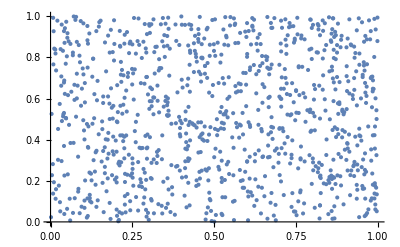

```mathematica
data3 = {0.4601736068725586,0.6826620101928711,0.030837059020996094,0.8405904769897461,0.5415334701538086,0.5086202621459961,0.4997549057006836,0.8321828842163086,0.9802694320678711,0.3526754379272461,0.6094503402709961,0.7386312484741211,0.6751089096069336,0.4622335433959961,0.8648519515991211,0.3025960922241211,0.9544363021850586,0.7155599594116211,0.3820791244506836,0.9605855941772461,0.028105735778808594,0.5739278793334961,0.8710775375366211,0.6445455551147461,0.4520559310913086,0.9380636215209961,0.3722677230834961,0.1333303451538086,0.5044088363647461,0.3561544418334961,0.5194082260131836,0.7752370834350586,0.0900411605834961,0.7767782211303711,0.8883657455444336,0.8860006332397461,0.2221212387084961,0.3930044174194336,0.5110311508178711,0.8720541000366211,0.7917928695678711,0.3245840072631836,0.2865743637084961,0.1190786361694336,0.2401113510131836,0.8212270736694336,0.2881460189819336,0.2394399642944336,0.3268728256225586,0.6632223129272461,0.015517234802246094,0.1126546859741211,0.9532461166381836,0.1748189926147461,0.3999471664428711,0.9995718002319336,0.9941396713256836,0.9363088607788086,0.1128988265991211,0.1142721176147461,0.3646078109741211,0.8428945541381836,0.1835165023803711,0.014403343200683594,0.8386831283569336,0.9665365219116211,0.6581716537475586,0.8053121566772461,0.5951528549194336,0.2437734603881836,0.056563377380371094,0.4721670150756836,0.7587881088256836,0.7522573471069336,0.032607078552246094,0.6625051498413086,0.8018636703491211,0.3086843490600586,0.2872915267944336,0.6724233627319336,0.7467336654663086,0.8915700912475586,0.4113759994506836,0.2615346908569336,0.1208639144897461,0.1004323959350586,0.9660482406616211,0.6128835678100586,0.8632345199584961,0.6979207992553711,0.3310079574584961,0.7368154525756836,0.3267202377319336,0.3207082748413086,0.8513936996459961,0.9955892562866211,0.1664724349975586,0.8730306625366211,0.4127187728881836,0.4965658187866211,0.6662740707397461,0.6033163070678711,0.1477804183959961,0.9502859115600586,0.3954610824584961,0.42659327387809753,0.3967275619506836,0.4158315658569336,0.0709676742553711,0.9994497299194336,0.8797597885131836,0.4269704818725586,0.8225545883178711,0.016676902770996094,0.1590566635131836,0.1898946762084961,0.3434743881225586,0.9920339584350586,0.4640951156616211,0.7987813949584961,0.9435720443725586,0.023070335388183594,0.4521780014038086,0.3374319076538086,0.9614706039428711,0.3334035873413086,0.7484273910522461,0.049910545349121094,0.8057088851928711,0.6661825180053711,0.4260244369506836,0.6334218978881836,0.8960866928100586,0.5233755111694336,0.2136068344116211,0.5649557113647461,0.8701009750366211,0.9246664047241211,0.5979604721069336,0.6676321029663086,0.7441854476928711,0.050642967224121094,0.0635976791381836,0.6332693099975586,0.8333272933959961,0.9296102523803711,0.7986898422241211,0.1849355697631836,0.6498250961303711,0.3184957504272461,0.7219533920288086,0.6739797592163086,0.4362173080444336,0.4741353988647461,0.011397361755371094,0.8431539535522461,0.3254537582397461,0.3405141830444336,0.3050069808959961,0.6538686752319336,0.1249685287475586,0.0948781967163086,0.0740041732788086,0.1152944564819336,0.3609457015991211,0.1576681137084961,0.4888753890991211,0.4609975814819336,0.7987051010131836,0.7926626205444336,0.5346822738647461,0.5229940414428711,0.039229393005371094,0.5234365463256836,0.1941671371459961,0.9810171127319336,0.7050924301147461,0.8294057846069336,0.2770681381225586,0.1915884017944336,0.4148397445678711,0.3880300521850586,0.6301565170288086,0.1057271957397461,0.2015981674194336,0.2163839340209961,0.6814107894897461,0.2661123275756836,0.8797140121459961,0.5255880355834961,0.1200399398803711,0.1158590316772461,0.4645833969116211,0.4303274154663086,0.9378805160522461,0.1562795639038086,0.2936697006225586,0.025481224060058594,0.1766195297241211,0.4330739974975586,0.4796590805053711,0.3937673568725586,0.8607015609741211,0.7369222640991211,0.0729970932006836,0.6670827865600586,0.5583486557006836,0.5290517807006836,0.5228719711303711,0.5589742660522461,0.2268209457397461,0.9103689193725586,0.6843862533569336,0.9916067123413086,0.1880788803100586,0.2272481918334961,0.0842580795288086,0.3172292709350586,0.8260641098022461,0.2133016586303711,0.4207906723022461,0.6969594955444336,0.2880849838256836,0.9626302719116211,0.6290426254272461,0.6255025863647461,0.3296804428100586,0.0863485336303711,0.8603811264038086,0.2088308334350586,0.009474754333496094,0.9276723861694336,0.2769002914428711,0.3583669662475586,0.5157766342163086,0.2543478012084961,0.5952291488647461,0.9258871078491211,0.2711324691772461,0.1739339828491211,0.3081655502319336,0.9616842269897461,0.6761007308959961,0.7656393051147461,0.3666677474975586,0.048033714294433594,0.9737691879272461,0.9805440902709961,0.2979574203491211,0.043974876403808594,0.9424428939819336,0.9905538558959961,0.4219808578491211,0.4712820053100586,0.4642324447631836,0.7954092025756836,0.9837026596069336,0.2353658676147461,0.1356496810913086,0.2448110580444336,0.2257528305053711,0.8672323226928711,0.8998708724975586,0.3512258529663086,0.5885305404663086,0.4256277084350586,0.4866781234741211,0.8078145980834961,0.0686483383178711,0.043700218200683594,0.6229543685913086,0.0780019760131836,0.5118398666381836,0.4465475082397461,0.2022237777709961,0.1920156478881836,0.5644826889038086,0.9647512435913086,0.2438650131225586,0.8771657943725586,0.2263631820678711,0.6038808822631836,0.007948875427246094,0.9929800033569336,0.0845174789428711,0.1472768783569336,0.4264059066772461,0.8334646224975586,0.7131185531616211,0.1305379867553711,0.7938528060913086,0.5467367172241211,0.6089925765991211,0.3169240951538086,0.6048269271850586,0.1236104965209961,0.2347249984741211,0.2294912338256836,0.046477317810058594,0.7695913314819336,0.7544851303100586,0.9930868148803711,0.060851097106933594,0.8661336898803711,0.6789083480834961,0.4037466049194336,0.6537008285522461,0.6557760238647461,0.2224874496459961,0.5701284408569336,0.4606771469116211,0.4238882064819336,0.9611349105834961,0.2530813217163086,0.1760549545288086,0.9065542221069336,0.6366109848022461,0.7343282699584961,1.8215179443359375E-4,0.2665548324584961,0.5210256576538086,0.4553213119506836,0.2433614730834961,0.1006765365600586,0.7176504135131836,0.3319692611694336,0.7917013168334961,0.8384237289428711,0.5967397689819336,0.7244253158569336,0.5222311019897461,0.8137502670288086,0.8251638412475586,0.2255239486694336,0.3091573715209961,0.5628347396850586,0.1022939682006836,0.4450216293334961,0.8023672103881836,0.5307607650756836,0.6727132797241211,0.0932149887084961,0.5652608871459961,0.6609334945678711,0.7873678207397461,0.7391805648803711,0.3966817855834961,0.4926595687866211,0.004302024841308594,0.2272634506225586,0.1254415512084961,0.2021017074584961,0.060057640075683594,0.007094383239746094,0.2811574935913086,0.3596487045288086,0.9936361312866211,0.6012563705444336,0.8170614242553711,0.9624624252319336,0.9048757553100586,0.8494100570678711,0.037886619567871094,0.8324422836303711,0.7949972152709961,0.4383535385131836,0.8691244125366211,0.4601888656616211,0.4846181869506836,0.4247732162475586,0.3065481185913086,0.2132253646850586,0.8527059555053711,0.7325429916381836,0.2843160629272461,0.2575979232788086,0.7422780990600586,0.9523305892944336,0.9713125228881836,0.4642477035522461,0.4014883041381836,0.9593954086303711,0.2313375473022461,0.4207601547241211,0.3695211410522461,0.4774465560913086,0.9366750717163086,0.5668630599975586,0.6298208236694336,0.8661947250366211,0.7973012924194336,0.4440145492553711,0.8173818588256836,0.2419576644897461,0.8681478500366211,0.016997337341308594,0.7369527816772461,0.3102712631225586,0.6460409164428711,0.4406728744506836,0.4699697494506836,0.8922262191772461,0.5460042953491211,0.2330160140991211,0.5369405746459961,0.9055471420288086,0.7574911117553711,0.1000661849975586,0.4947042465209961,0.9822072982788086,0.1144552230834961,0.8671712875366211,0.2150716781616211,0.7163228988647461,0.7435293197631836,0.5820302963256836,0.6357717514038086,0.4724569320678711,0.7588644027709961,0.7571249008178711,0.2604665756225586,0.3877706527709961,0.2721242904663086,0.3609609603881836,0.9395895004272461,0.2510366439819336,0.2151479721069336,0.7784719467163086,0.6058950424194336,0.9287557601928711,0.6424245834350586,0.8652181625366211,0.5876455307006836,0.1660909652709961,0.2678518295288086,0.2911367416381836,0.8439626693725586,0.4011373519897461,0.6916952133178711,0.3572988510131836,0.8570394515991211,0.8831777572631836,0.5733175277709961,0.6353139877319336,0.1712331771850586,0.1491079330444336,0.9718465805053711,0.060988426208496094,0.3838796615600586,0.2689657211303711,0.9897298812866211,0.8025045394897461,0.9587240219116211,0.1624746322631836,0.047499656677246094,0.5035848617553711,0.8080434799194336,0.4456014633178711,0.1748495101928711,0.2116994857788086,0.9292287826538086,0.2919607162475586,0.058562278747558594,0.1128225326538086,0.8836355209350586,0.6802511215209961,0.4590749740600586,0.3398733139038086,0.0781850814819336,0.9975423812866211,0.1340780258178711,0.6216726303100586,0.7632741928100586,0.1437368392944336,0.6860494613647461,0.3466787338256836,0.8540029525756836,0.4992666244506836,0.8642416000366211,0.9902791976928711,0.1139211654663086,0.028761863708496094,0.0958852767944336,0.6483449935913086,0.6700277328491211,0.6087484359741211,0.2106618881225586,0.047194480895996094,0.5055532455444336,0.033659934997558594,0.2959127426147461,0.3616476058959961,0.5188741683959961,0.5340261459350586,0.1199026107788086,0.1315908432006836,0.3002614974975586,0.010191917419433594,0.1930227279663086,0.3273611068725586,0.5893545150756836,0.7251272201538086,0.9080343246459961,0.3801717758178711,0.034819602966308594,0.4907064437866211,0.053404808044433594,0.6167593002319336,0.9916830062866211,0.3567953109741211,0.9044790267944336,0.3015737533569336,0.9621419906616211,0.1133260726928711,0.7508230209350586,0.6365957260131836,0.3479146957397461,0.9087209701538086,0.3575735092163086,0.2123403549194336,0.8566274642944336,0.2508077621459961,0.2577047348022461,0.4417715072631836,0.9053335189819336,0.7092123031616211,0.4558706283569336,0.4122762680053711,0.3564596176147461,0.5676412582397461,0.4810628890991211,0.0704336166381836,0.3844442367553711,0.8805685043334961,0.3306112289428711,0.3493947982788086,0.8026571273803711,0.2896108627319336,0.1583700180053711,0.4514455795288086,0.8899679183959961,0.9054098129272461,0.5487508773803711,0.9557180404663086,0.3034963607788086,0.5874776840209961,0.2027730941772461,0.4887533187866211,0.1050863265991211,0.5814199447631836,0.6698751449584961,0.3161153793334961,0.041884422302246094,0.6878957748413086,0.0827779769897461,0.6629781723022461,0.9969472885131836,0.5005178451538086,0.0014638900756835938,0.022826194763183594,0.3021230697631836,0.5500020980834961,0.9965353012084961,0.3247060775756836,0.8524312973022461,0.1901082992553711,0.8261861801147461,0.1402578353881836,0.0731954574584961,0.5935811996459961,0.3516378402709961,0.9643087387084961,0.034117698669433594,0.9600820541381836,0.7362661361694336,0.5234670639038086,0.2978963851928711,0.6202688217163086,0.9316701889038086,0.4144887924194336,0.4300222396850586,0.9577016830444336,0.7768697738647461,0.2941579818725586,0.3580465316772461,0.5816793441772461,0.1993703842163086,0.3959188461303711,0.4567708969116211,0.2111654281616211,0.2747945785522461,0.2075643539428711,0.2839803695678711,0.8766164779663086,0.1186513900756836,0.9168539047241211,0.2275686264038086,0.1940603256225586,0.7853231430053711,0.5432424545288086,0.2922964096069336,0.2044210433959961,0.4852743148803711,0.1420125961303711,0.5917654037475586,0.1658010482788086,0.3630514144897461,0.7116537094116211,0.4411916732788086,0.8322286605834961,0.6433248519897461,0.041167259216308594,0.3694448471069336,0.2762441635131836,0.6752004623413086,0.9439077377319336,0.4536581039428711,0.7308187484741211,0.9676198959350586,0.7670583724975586,0.9070272445678711,0.3832998275756836,0.4800710678100586,0.7730245590209961,0.6262655258178711,0.2072591781616211,0.0032186508178710938,0.5253591537475586,0.033019065856933594,0.7077474594116211,0.9444112777709961,0.8192434310913086,0.9363546371459961,0.9320821762084961,0.8216238021850586,0.6627950668334961,0.7506093978881836,0.6406240463256836,0.7587575912475586,0.5299062728881836,0.4788656234741211,0.7005910873413086,0.4562826156616211,0.9973440170288086,0.051802635192871094,0.9180746078491211,0.8632650375366211,0.9906148910522461,0.1379995346069336,0.3384695053100586,0.7480764389038086,0.4946126937866211,0.6122274398803711,0.1442556381225586,0.1048421859741211,0.6755361557006836,0.1405630111694336,0.3460988998413086,0.5606832504272461,0.9901418685913086,0.9877767562866211,0.6468191146850586,0.8071432113647461,0.5139150619506836,0.6757040023803711,0.5094289779663086,0.4217977523803711,0.5596303939819336,0.3605642318725586,0.5409688949584961,0.5987997055053711,0.8998556137084961,0.4384145736694336,0.7291097640991211,0.9472799301147461,0.4170064926147461,0.3531332015991211,0.0682516098022461,0.8107595443725586,0.2710561752319336,0.8613119125366211,0.9377889633178711,0.2791280746459961,0.7975149154663086,0.8427114486694336,0.8607168197631836,0.1608572006225586,0.5785360336303711,0.4735250473022461,0.2552175521850586,0.9921560287475586,0.1758718490600586,0.6102437973022461,0.7516622543334961,0.5314168930053711,0.8622884750366211,0.4471578598022461,0.7796316146850586,0.4870901107788086,0.8619985580444336,0.015181541442871094,0.8193655014038086,0.9548177719116211,0.1610403060913086,0.6101675033569336,0.4620656967163086,0.2493124008178711,0.2363729476928711,0.7054891586303711,0.5982046127319336,0.5631551742553711,0.9582357406616211,0.7609243392944336,0.6169424057006836,0.9543294906616211,0.7046194076538086,0.1968679428100586,0.2057943344116211,0.5342702865600586,0.9964284896850586,0.5432119369506836,0.8592214584350586,0.9158926010131836,0.1299581527709961,0.7940511703491211,0.9849691390991211,0.6350393295288086,0.5448598861694336,0.7038412094116211,0.8676900863647461,0.0760183334350586,0.9827718734741211,0.5578603744506836,0.0983419418334961,0.7465963363647461,0.8829641342163086,0.5816640853881836,0.4690084457397461,0.3952932357788086,0.2496786117553711,0.6685934066772461,0.7179403305053711,0.9858236312866211,0.6887350082397461,0.007826805114746094,0.1376485824584961,0.1807851791381836,0.0923147201538086,0.9771566390991211,0.8882131576538086,0.1774587631225586,0.3319387435913086,0.5329885482788086,0.2038717269897461,0.6652212142944336,0.3714895248413086,0.1688070297241211,0.4019308090209961,0.2159566879272461,0.2901449203491211,0.4182882308959961,0.6649007797241211,0.3141469955444336,0.6054220199584961,0.4848470687866211,0.6290273666381836,0.7185506820678711,0.8867330551147461,0.8497304916381836,0.2033529281616211,0.029692649841308594,0.051344871520996094,0.8958883285522461,0.0853414535522461,0.1608877182006836,0.3448934555053711,0.1951894760131836,0.8657979965209961,0.8374166488647461,0.8354024887084961,0.1873159408569336,0.5555410385131836,0.4111623764038086,0.9585714340209961,0.8766317367553711,0.4515829086303711,0.4841451644897461,0.2609548568725586,0.8187856674194336,0.2610616683959961,0.4868001937866211,0.1113271713256836,0.4765157699584961,0.042098045349121094,0.038420677185058594,0.5133199691772461,0.2677755355834961,0.055266380310058594,0.8787984848022461,0.5767049789428711,0.4098501205444336,0.1276540756225586,0.7064352035522461,0.3587942123413086,0.6011800765991211,0.2947835922241211,0.7053060531616211,0.5608358383178711,0.008742332458496094,0.7662954330444336,0.8926687240600586,0.4465932846069336,0.4589529037475586,0.7184133529663086,0.7006521224975586,0.2277517318725586,0.2338552474975586,0.9235982894897461,0.6166372299194336,0.1281881332397461,0.4775533676147461,0.2492818832397461,0.7443532943725586,0.8723592758178711,0.9084615707397461,0.8921346664428711,0.5381002426147461,0.8979635238647461,0.5338888168334961,0.5285634994506836,0.9362020492553711,0.1800680160522461,0.5755147933959961,0.6737356185913086,0.9678640365600586,0.042830467224121094,0.8712301254272461,0.1844167709350586,0.9345693588256836,0.7327413558959961,0.5186758041381836,0.3416128158569336,0.8787221908569336,0.9646749496459961,0.5788869857788086,0.2525014877319336,0.7227315902709961,0.6221914291381836,0.9838705062866211,0.7070608139038086,0.7033224105834961,0.6009359359741211,0.8031759262084961,0.2510671615600586,0.2840719223022461,0.0891408920288086,0.042387962341308594,0.2255544662475586,0.3583211898803711,0.0885000228881836,0.8087759017944336,0.6462392807006836,0.1661214828491211,0.2368917465209961,0.7247610092163086,0.4129476547241211,0.5371847152709961,0.5389242172241211,0.2796621322631836,0.1699209213256836,0.7324819564819336,0.6173696517944336,0.9491567611694336,0.6008901596069336,0.2928152084350586,0.8238668441772461,0.2194814682006836,0.4210958480834961,0.2964162826538086,0.4252309799194336,0.0804128646850586,0.7210683822631836,0.8583822250366211,0.2252035140991211,0.4141683578491211,0.2194814682006836,0.5265035629272461,0.6997518539428711,0.7644186019897461,0.3092031478881836,0.2097005844116211,0.2928152084350586,0.7048330307006836,0.6479482650756836,0.7720632553100586,0.041075706481933594,0.9282369613647461,0.8528890609741211,0.2184438705444336,0.7393789291381836,0.1400136947631836,0.9282369613647461,0.6997518539428711,0.6094655990600586,0.4720144271850586,0.7210683822631836,0.8174734115600586,0.8238668441772461,0.5028371810913086,0.9855489730834961,0.4210958480834961,0.1901845932006836,0.5028371810913086,0.4523763656616211,0.8759756088256836,0.7048330307006836,0.9791402816772461,0.9282369613647461,0.2230825424194336,0.7132863998413086,0.6479482650756836,0.3155050277709961,0.3038625717163086,0.9195547103881836,0.8593587875366211,0.052733421325683594,0.2313680648803711,0.6393117904663086,0.9136648178100586,0.9855489730834961,0.6479482650756836,0.5796499252319336,0.9195547103881836,0.2501363754272461,0.3092031478881836,0.1038351058959961,0.4012136459350586,0.4800100326538086,0.9442892074584961,0.7644643783569336,0.1531209945678711,0.9791402816772461,0.6997518539428711,0.4528646469116211,0.9136648178100586,0.6247854232788086,0.2948446273803711,0.9136648178100586,0.3415975570678711,0.4209432601928711,0.8583822250366211,0.8759756088256836,0.8603353500366211,0.7551870346069336,0.9125967025756836,0.4252309799194336,0.7644643783569336,0.3038625717163086,0.4120626449584961,0.2948446273803711,0.3074483871459961,0.1110525131225586,0.020934104919433594,0.9791402816772461,0.1038351058959961,0.1038351058959961,0.0683736801147461,0.8238668441772461,0.0804128646850586,0.8759756088256836,0.8238668441772461,0.0804128646850586,0.6008901596069336,0.9672536849975586,0.8881063461303711,0.3147420883178711,0.9855489730834961,0.1809377670288086,0.8238668441772461,0.9082784652709961,0.2501363754272461,0.8636159896850586,0.2184438705444336,0.041075706481933594,0.5300741195678711,0.4523763656616211,0.1809377670288086,0.5004568099975586,0.3147420883178711,0.5237417221069336,0.4824666976928711,0.2018880844116211,0.3415975570678711,0.041075706481933594,0.6780385971069336,0.9442892074584961,0.4209432601928711,0.3092489242553711,0.5871572494506836};

data4 = {0.6826620101928711,0.030837059020996094,0.8405904769897461,0.5415334701538086,0.5086202621459961,0.4997549057006836,0.8321828842163086,0.9802694320678711,0.3526754379272461,0.6094503402709961,0.7386312484741211,0.6751089096069336,0.4622335433959961,0.8648519515991211,0.3025960922241211,0.9544363021850586,0.7155599594116211,0.3820791244506836,0.9605855941772461,0.028105735778808594,0.5739278793334961,0.8710775375366211,0.6445455551147461,0.4520559310913086,0.9380636215209961,0.3722677230834961,0.1333303451538086,0.5044088363647461,0.3561544418334961,0.5194082260131836,0.7752370834350586,0.0900411605834961,0.7767782211303711,0.8883657455444336,0.8860006332397461,0.2221212387084961,0.3930044174194336,0.5110311508178711,0.8720541000366211,0.7917928695678711,0.3245840072631836,0.2865743637084961,0.1190786361694336,0.2401113510131836,0.8212270736694336,0.2881460189819336,0.2394399642944336,0.3268728256225586,0.6632223129272461,0.015517234802246094,0.1126546859741211,0.9532461166381836,0.1748189926147461,0.3999471664428711,0.9995718002319336,0.9941396713256836,0.9363088607788086,0.1128988265991211,0.1142721176147461,0.3646078109741211,0.8428945541381836,0.1835165023803711,0.014403343200683594,0.8386831283569336,0.9665365219116211,0.6581716537475586,0.8053121566772461,0.5951528549194336,0.2437734603881836,0.056563377380371094,0.4721670150756836,0.7587881088256836,0.7522573471069336,0.032607078552246094,0.6625051498413086,0.8018636703491211,0.3086843490600586,0.2872915267944336,0.6724233627319336,0.7467336654663086,0.8915700912475586,0.4113759994506836,0.2615346908569336,0.1208639144897461,0.1004323959350586,0.9660482406616211,0.6128835678100586,0.8632345199584961,0.6979207992553711,0.3310079574584961,0.7368154525756836,0.3267202377319336,0.3207082748413086,0.8513936996459961,0.9955892562866211,0.1664724349975586,0.8730306625366211,0.4127187728881836,0.4965658187866211,0.6662740707397461,0.6033163070678711,0.1477804183959961,0.9502859115600586,0.3954610824584961,0.42659327387809753,0.3967275619506836,0.4158315658569336,0.0709676742553711,0.9994497299194336,0.8797597885131836,0.4269704818725586,0.8225545883178711,0.016676902770996094,0.1590566635131836,0.1898946762084961,0.3434743881225586,0.9920339584350586,0.4640951156616211,0.7987813949584961,0.9435720443725586,0.023070335388183594,0.4521780014038086,0.3374319076538086,0.9614706039428711,0.3334035873413086,0.7484273910522461,0.049910545349121094,0.8057088851928711,0.6661825180053711,0.4260244369506836,0.6334218978881836,0.8960866928100586,0.5233755111694336,0.2136068344116211,0.5649557113647461,0.8701009750366211,0.9246664047241211,0.5979604721069336,0.6676321029663086,0.7441854476928711,0.050642967224121094,0.0635976791381836,0.6332693099975586,0.8333272933959961,0.9296102523803711,0.7986898422241211,0.1849355697631836,0.6498250961303711,0.3184957504272461,0.7219533920288086,0.6739797592163086,0.4362173080444336,0.4741353988647461,0.011397361755371094,0.8431539535522461,0.3254537582397461,0.3405141830444336,0.3050069808959961,0.6538686752319336,0.1249685287475586,0.0948781967163086,0.0740041732788086,0.1152944564819336,0.3609457015991211,0.1576681137084961,0.4888753890991211,0.4609975814819336,0.7987051010131836,0.7926626205444336,0.5346822738647461,0.5229940414428711,0.039229393005371094,0.5234365463256836,0.1941671371459961,0.9810171127319336,0.7050924301147461,0.8294057846069336,0.2770681381225586,0.1915884017944336,0.4148397445678711,0.3880300521850586,0.6301565170288086,0.1057271957397461,0.2015981674194336,0.2163839340209961,0.6814107894897461,0.2661123275756836,0.8797140121459961,0.5255880355834961,0.1200399398803711,0.1158590316772461,0.4645833969116211,0.4303274154663086,0.9378805160522461,0.1562795639038086,0.2936697006225586,0.025481224060058594,0.1766195297241211,0.4330739974975586,0.4796590805053711,0.3937673568725586,0.8607015609741211,0.7369222640991211,0.0729970932006836,0.6670827865600586,0.5583486557006836,0.5290517807006836,0.5228719711303711,0.5589742660522461,0.2268209457397461,0.9103689193725586,0.6843862533569336,0.9916067123413086,0.1880788803100586,0.2272481918334961,0.0842580795288086,0.3172292709350586,0.8260641098022461,0.2133016586303711,0.4207906723022461,0.6969594955444336,0.2880849838256836,0.9626302719116211,0.6290426254272461,0.6255025863647461,0.3296804428100586,0.0863485336303711,0.8603811264038086,0.2088308334350586,0.009474754333496094,0.9276723861694336,0.2769002914428711,0.3583669662475586,0.5157766342163086,0.2543478012084961,0.5952291488647461,0.9258871078491211,0.2711324691772461,0.1739339828491211,0.3081655502319336,0.9616842269897461,0.6761007308959961,0.7656393051147461,0.3666677474975586,0.048033714294433594,0.9737691879272461,0.9805440902709961,0.2979574203491211,0.043974876403808594,0.9424428939819336,0.9905538558959961,0.4219808578491211,0.4712820053100586,0.4642324447631836,0.7954092025756836,0.9837026596069336,0.2353658676147461,0.1356496810913086,0.2448110580444336,0.2257528305053711,0.8672323226928711,0.8998708724975586,0.3512258529663086,0.5885305404663086,0.4256277084350586,0.4866781234741211,0.8078145980834961,0.0686483383178711,0.043700218200683594,0.6229543685913086,0.0780019760131836,0.5118398666381836,0.4465475082397461,0.2022237777709961,0.1920156478881836,0.5644826889038086,0.9647512435913086,0.2438650131225586,0.8771657943725586,0.2263631820678711,0.6038808822631836,0.007948875427246094,0.9929800033569336,0.0845174789428711,0.1472768783569336,0.4264059066772461,0.8334646224975586,0.7131185531616211,0.1305379867553711,0.7938528060913086,0.5467367172241211,0.6089925765991211,0.3169240951538086,0.6048269271850586,0.1236104965209961,0.2347249984741211,0.2294912338256836,0.046477317810058594,0.7695913314819336,0.7544851303100586,0.9930868148803711,0.060851097106933594,0.8661336898803711,0.6789083480834961,0.4037466049194336,0.6537008285522461,0.6557760238647461,0.2224874496459961,0.5701284408569336,0.4606771469116211,0.4238882064819336,0.9611349105834961,0.2530813217163086,0.1760549545288086,0.9065542221069336,0.6366109848022461,0.7343282699584961,1.8215179443359375E-4,0.2665548324584961,0.5210256576538086,0.4553213119506836,0.2433614730834961,0.1006765365600586,0.7176504135131836,0.3319692611694336,0.7917013168334961,0.8384237289428711,0.5967397689819336,0.7244253158569336,0.5222311019897461,0.8137502670288086,0.8251638412475586,0.2255239486694336,0.3091573715209961,0.5628347396850586,0.1022939682006836,0.4450216293334961,0.8023672103881836,0.5307607650756836,0.6727132797241211,0.0932149887084961,0.5652608871459961,0.6609334945678711,0.7873678207397461,0.7391805648803711,0.3966817855834961,0.4926595687866211,0.004302024841308594,0.2272634506225586,0.1254415512084961,0.2021017074584961,0.060057640075683594,0.007094383239746094,0.2811574935913086,0.3596487045288086,0.9936361312866211,0.6012563705444336,0.8170614242553711,0.9624624252319336,0.9048757553100586,0.8494100570678711,0.037886619567871094,0.8324422836303711,0.7949972152709961,0.4383535385131836,0.8691244125366211,0.4601888656616211,0.4846181869506836,0.4247732162475586,0.3065481185913086,0.2132253646850586,0.8527059555053711,0.7325429916381836,0.2843160629272461,0.2575979232788086,0.7422780990600586,0.9523305892944336,0.9713125228881836,0.4642477035522461,0.4014883041381836,0.9593954086303711,0.2313375473022461,0.4207601547241211,0.3695211410522461,0.4774465560913086,0.9366750717163086,0.5668630599975586,0.6298208236694336,0.8661947250366211,0.7973012924194336,0.4440145492553711,0.8173818588256836,0.2419576644897461,0.8681478500366211,0.016997337341308594,0.7369527816772461,0.3102712631225586,0.6460409164428711,0.4406728744506836,0.4699697494506836,0.8922262191772461,0.5460042953491211,0.2330160140991211,0.5369405746459961,0.9055471420288086,0.7574911117553711,0.1000661849975586,0.4947042465209961,0.9822072982788086,0.1144552230834961,0.8671712875366211,0.2150716781616211,0.7163228988647461,0.7435293197631836,0.5820302963256836,0.6357717514038086,0.4724569320678711,0.7588644027709961,0.7571249008178711,0.2604665756225586,0.3877706527709961,0.2721242904663086,0.3609609603881836,0.9395895004272461,0.2510366439819336,0.2151479721069336,0.7784719467163086,0.6058950424194336,0.9287557601928711,0.6424245834350586,0.8652181625366211,0.5876455307006836,0.1660909652709961,0.2678518295288086,0.2911367416381836,0.8439626693725586,0.4011373519897461,0.6916952133178711,0.3572988510131836,0.8570394515991211,0.8831777572631836,0.5733175277709961,0.6353139877319336,0.1712331771850586,0.1491079330444336,0.9718465805053711,0.060988426208496094,0.3838796615600586,0.2689657211303711,0.9897298812866211,0.8025045394897461,0.9587240219116211,0.1624746322631836,0.047499656677246094,0.5035848617553711,0.8080434799194336,0.4456014633178711,0.1748495101928711,0.2116994857788086,0.9292287826538086,0.2919607162475586,0.058562278747558594,0.1128225326538086,0.8836355209350586,0.6802511215209961,0.4590749740600586,0.3398733139038086,0.0781850814819336,0.9975423812866211,0.1340780258178711,0.6216726303100586,0.7632741928100586,0.1437368392944336,0.6860494613647461,0.3466787338256836,0.8540029525756836,0.4992666244506836,0.8642416000366211,0.9902791976928711,0.1139211654663086,0.028761863708496094,0.0958852767944336,0.6483449935913086,0.6700277328491211,0.6087484359741211,0.2106618881225586,0.047194480895996094,0.5055532455444336,0.033659934997558594,0.2959127426147461,0.3616476058959961,0.5188741683959961,0.5340261459350586,0.1199026107788086,0.1315908432006836,0.3002614974975586,0.010191917419433594,0.1930227279663086,0.3273611068725586,0.5893545150756836,0.7251272201538086,0.9080343246459961,0.3801717758178711,0.034819602966308594,0.4907064437866211,0.053404808044433594,0.6167593002319336,0.9916830062866211,0.3567953109741211,0.9044790267944336,0.3015737533569336,0.9621419906616211,0.1133260726928711,0.7508230209350586,0.6365957260131836,0.3479146957397461,0.9087209701538086,0.3575735092163086,0.2123403549194336,0.8566274642944336,0.2508077621459961,0.2577047348022461,0.4417715072631836,0.9053335189819336,0.7092123031616211,0.4558706283569336,0.4122762680053711,0.3564596176147461,0.5676412582397461,0.4810628890991211,0.0704336166381836,0.3844442367553711,0.8805685043334961,0.3306112289428711,0.3493947982788086,0.8026571273803711,0.2896108627319336,0.1583700180053711,0.4514455795288086,0.8899679183959961,0.9054098129272461,0.5487508773803711,0.9557180404663086,0.3034963607788086,0.5874776840209961,0.2027730941772461,0.4887533187866211,0.1050863265991211,0.5814199447631836,0.6698751449584961,0.3161153793334961,0.041884422302246094,0.6878957748413086,0.0827779769897461,0.6629781723022461,0.9969472885131836,0.5005178451538086,0.0014638900756835938,0.022826194763183594,0.3021230697631836,0.5500020980834961,0.9965353012084961,0.3247060775756836,0.8524312973022461,0.1901082992553711,0.8261861801147461,0.1402578353881836,0.0731954574584961,0.5935811996459961,0.3516378402709961,0.9643087387084961,0.034117698669433594,0.9600820541381836,0.7362661361694336,0.5234670639038086,0.2978963851928711,0.6202688217163086,0.9316701889038086,0.4144887924194336,0.4300222396850586,0.9577016830444336,0.7768697738647461,0.2941579818725586,0.3580465316772461,0.5816793441772461,0.1993703842163086,0.3959188461303711,0.4567708969116211,0.2111654281616211,0.2747945785522461,0.2075643539428711,0.2839803695678711,0.8766164779663086,0.1186513900756836,0.9168539047241211,0.2275686264038086,0.1940603256225586,0.7853231430053711,0.5432424545288086,0.2922964096069336,0.2044210433959961,0.4852743148803711,0.1420125961303711,0.5917654037475586,0.1658010482788086,0.3630514144897461,0.7116537094116211,0.4411916732788086,0.8322286605834961,0.6433248519897461,0.041167259216308594,0.3694448471069336,0.2762441635131836,0.6752004623413086,0.9439077377319336,0.4536581039428711,0.7308187484741211,0.9676198959350586,0.7670583724975586,0.9070272445678711,0.3832998275756836,0.4800710678100586,0.7730245590209961,0.6262655258178711,0.2072591781616211,0.0032186508178710938,0.5253591537475586,0.033019065856933594,0.7077474594116211,0.9444112777709961,0.8192434310913086,0.9363546371459961,0.9320821762084961,0.8216238021850586,0.6627950668334961,0.7506093978881836,0.6406240463256836,0.7587575912475586,0.5299062728881836,0.4788656234741211,0.7005910873413086,0.4562826156616211,0.9973440170288086,0.051802635192871094,0.9180746078491211,0.8632650375366211,0.9906148910522461,0.1379995346069336,0.3384695053100586,0.7480764389038086,0.4946126937866211,0.6122274398803711,0.1442556381225586,0.1048421859741211,0.6755361557006836,0.1405630111694336,0.3460988998413086,0.5606832504272461,0.9901418685913086,0.9877767562866211,0.6468191146850586,0.8071432113647461,0.5139150619506836,0.6757040023803711,0.5094289779663086,0.4217977523803711,0.5596303939819336,0.3605642318725586,0.5409688949584961,0.5987997055053711,0.8998556137084961,0.4384145736694336,0.7291097640991211,0.9472799301147461,0.4170064926147461,0.3531332015991211,0.0682516098022461,0.8107595443725586,0.2710561752319336,0.8613119125366211,0.9377889633178711,0.2791280746459961,0.7975149154663086,0.8427114486694336,0.8607168197631836,0.1608572006225586,0.5785360336303711,0.4735250473022461,0.2552175521850586,0.9921560287475586,0.1758718490600586,0.6102437973022461,0.7516622543334961,0.5314168930053711,0.8622884750366211,0.4471578598022461,0.7796316146850586,0.4870901107788086,0.8619985580444336,0.015181541442871094,0.8193655014038086,0.9548177719116211,0.1610403060913086,0.6101675033569336,0.4620656967163086,0.2493124008178711,0.2363729476928711,0.7054891586303711,0.5982046127319336,0.5631551742553711,0.9582357406616211,0.7609243392944336,0.6169424057006836,0.9543294906616211,0.7046194076538086,0.1968679428100586,0.2057943344116211,0.5342702865600586,0.9964284896850586,0.5432119369506836,0.8592214584350586,0.9158926010131836,0.1299581527709961,0.7940511703491211,0.9849691390991211,0.6350393295288086,0.5448598861694336,0.7038412094116211,0.8676900863647461,0.0760183334350586,0.9827718734741211,0.5578603744506836,0.0983419418334961,0.7465963363647461,0.8829641342163086,0.5816640853881836,0.4690084457397461,0.3952932357788086,0.2496786117553711,0.6685934066772461,0.7179403305053711,0.9858236312866211,0.6887350082397461,0.007826805114746094,0.1376485824584961,0.1807851791381836,0.0923147201538086,0.9771566390991211,0.8882131576538086,0.1774587631225586,0.3319387435913086,0.5329885482788086,0.2038717269897461,0.6652212142944336,0.3714895248413086,0.1688070297241211,0.4019308090209961,0.2159566879272461,0.2901449203491211,0.4182882308959961,0.6649007797241211,0.3141469955444336,0.6054220199584961,0.4848470687866211,0.6290273666381836,0.7185506820678711,0.8867330551147461,0.8497304916381836,0.2033529281616211,0.029692649841308594,0.051344871520996094,0.8958883285522461,0.0853414535522461,0.1608877182006836,0.3448934555053711,0.1951894760131836,0.8657979965209961,0.8374166488647461,0.8354024887084961,0.1873159408569336,0.5555410385131836,0.4111623764038086,0.9585714340209961,0.8766317367553711,0.4515829086303711,0.4841451644897461,0.2609548568725586,0.8187856674194336,0.2610616683959961,0.4868001937866211,0.1113271713256836,0.4765157699584961,0.042098045349121094,0.038420677185058594,0.5133199691772461,0.2677755355834961,0.055266380310058594,0.8787984848022461,0.5767049789428711,0.4098501205444336,0.1276540756225586,0.7064352035522461,0.3587942123413086,0.6011800765991211,0.2947835922241211,0.7053060531616211,0.5608358383178711,0.008742332458496094,0.7662954330444336,0.8926687240600586,0.4465932846069336,0.4589529037475586,0.7184133529663086,0.7006521224975586,0.2277517318725586,0.2338552474975586,0.9235982894897461,0.6166372299194336,0.1281881332397461,0.4775533676147461,0.2492818832397461,0.7443532943725586,0.8723592758178711,0.9084615707397461,0.8921346664428711,0.5381002426147461,0.8979635238647461,0.5338888168334961,0.5285634994506836,0.9362020492553711,0.1800680160522461,0.5755147933959961,0.6737356185913086,0.9678640365600586,0.042830467224121094,0.8712301254272461,0.1844167709350586,0.9345693588256836,0.7327413558959961,0.5186758041381836,0.3416128158569336,0.8787221908569336,0.9646749496459961,0.5788869857788086,0.2525014877319336,0.7227315902709961,0.6221914291381836,0.9838705062866211,0.7070608139038086,0.7033224105834961,0.6009359359741211,0.8031759262084961,0.2510671615600586,0.2840719223022461,0.0891408920288086,0.042387962341308594,0.2255544662475586,0.3583211898803711,0.0885000228881836,0.8087759017944336,0.6462392807006836,0.1661214828491211,0.2368917465209961,0.7247610092163086,0.4129476547241211,0.5371847152709961,0.5389242172241211,0.2796621322631836,0.1699209213256836,0.7324819564819336,0.6173696517944336,0.9491567611694336,0.6008901596069336,0.2928152084350586,0.8238668441772461,0.2194814682006836,0.4210958480834961,0.2964162826538086,0.4252309799194336,0.0804128646850586,0.7210683822631836,0.8583822250366211,0.2252035140991211,0.4141683578491211,0.2194814682006836,0.5265035629272461,0.6997518539428711,0.7644186019897461,0.3092031478881836,0.2097005844116211,0.2928152084350586,0.7048330307006836,0.6479482650756836,0.7720632553100586,0.041075706481933594,0.9282369613647461,0.8528890609741211,0.2184438705444336,0.7393789291381836,0.1400136947631836,0.9282369613647461,0.6997518539428711,0.6094655990600586,0.4720144271850586,0.7210683822631836,0.8174734115600586,0.8238668441772461,0.5028371810913086,0.9855489730834961,0.4210958480834961,0.1901845932006836,0.5028371810913086,0.4523763656616211,0.8759756088256836,0.7048330307006836,0.9791402816772461,0.9282369613647461,0.2230825424194336,0.7132863998413086,0.6479482650756836,0.3155050277709961,0.3038625717163086,0.9195547103881836,0.8593587875366211,0.052733421325683594,0.2313680648803711,0.6393117904663086,0.9136648178100586,0.9855489730834961,0.6479482650756836,0.5796499252319336,0.9195547103881836,0.2501363754272461,0.3092031478881836,0.1038351058959961,0.4012136459350586,0.4800100326538086,0.9442892074584961,0.7644643783569336,0.1531209945678711,0.9791402816772461,0.6997518539428711,0.4528646469116211,0.9136648178100586,0.6247854232788086,0.2948446273803711,0.9136648178100586,0.3415975570678711,0.4209432601928711,0.8583822250366211,0.8759756088256836,0.8603353500366211,0.7551870346069336,0.9125967025756836,0.4252309799194336,0.7644643783569336,0.3038625717163086,0.4120626449584961,0.2948446273803711,0.3074483871459961,0.1110525131225586,0.020934104919433594,0.9791402816772461,0.1038351058959961,0.1038351058959961,0.0683736801147461,0.8238668441772461,0.0804128646850586,0.8759756088256836,0.8238668441772461,0.0804128646850586,0.6008901596069336,0.9672536849975586,0.8881063461303711,0.3147420883178711,0.9855489730834961,0.1809377670288086,0.8238668441772461,0.9082784652709961,0.2501363754272461,0.8636159896850586,0.2184438705444336,0.041075706481933594,0.5300741195678711,0.4523763656616211,0.1809377670288086,0.5004568099975586,0.3147420883178711,0.5237417221069336,0.4824666976928711,0.2018880844116211,0.3415975570678711,0.041075706481933594,0.6780385971069336,0.9442892074584961,0.4209432601928711,0.3092489242553711,0.5871572494506836,0.5300741195678711};

ListPlot[Transpose[{data3, data4}]]
```

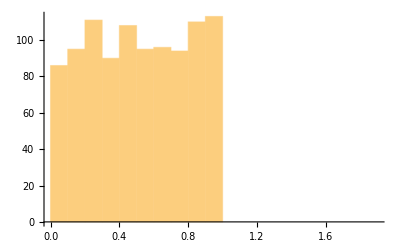

```mathematica
Histogram[data1]
```

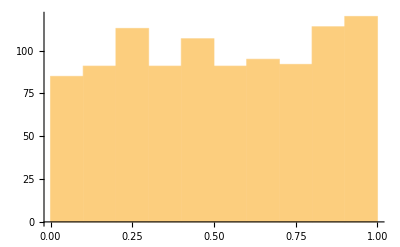

```mathematica
Histogram[data3]
```